Basic model:

```mathematica
system={
D[p1[t], t]==-ks m32[t]p1[t]+ kun (1-p1[t]),
D[m1[t], t]==(1-α)kon p1[t]-kdm m1[t]-kdim(m1[t])^2,
D[m12[t], t]==kdim(m1[t])^2-kdm m12[t]+α kon p1[t],


D[p2[t], t]==-ks m12[t]p2[t]+ kun (1- p2[t]),
D[m2[t], t]==(1-α)kon p2[t]-kdm m2[t]-kdim(m2[t])^2,
D[m22[t], t]==kdim(m2[t])^2-kdm m22[t]+α kon p2[t],


D[p3[t], t]==-ks m22[t]p3[t]+ (1-p3[t]) kun  ,
D[m3[t], t]==(1-α)kon p3[t]-kdm m3[t]-kdim(m3[t])^2,
D[m32[t], t]==kdim(m3[t])^2-kdm m32[t]+α kon p3[t]}
```

{p1'[t]==kun (1-p1[t])-ks m32[t] p1[t],m1'[t]==-kdm m1[t]-kdim m1[t]^2+kon (1-α) p1[t],m12'[t]==kdim m1[t]^2-kdm m12[t]+kon α p1[t],p2'[t]==kun (1-p2[t])-ks m12[t] p2[t],m2'[t]==-kdm m2[t]-kdim m2[t]^2+kon (1-α) p2[t],m22'[t]==kdim m2[t]^2-kdm m22[t]+kon α p2[t],p3'[t]==kun (1-p3[t])-ks m22[t] p3[t],m3'[t]==-kdm m3[t]-kdim m3[t]^2+kon (1-α) p3[t],m32'[t]==kdim m3[t]^2-kdm m32[t]+kon α p3[t]}

```mathematica
D[m1[t], t]==(1-α)kon p1[t]-kdm m1[t]-kdim(m1[t])^2
```

{p1'[t]==kun (1-p1[t])-ks m32[t] p1[t],m1'[t]==-kdm m1[t]-kdim m1[t]^2+kon (1-α) p1[t],m12'[t]==kdim m1[t]^2-kdm m12[t]+kon α p1[t],p2'[t]==kun (1-p2[t])-ks m12[t] p2[t],m2'[t]==-kdm m2[t]-kdim m2[t]^2+kon (1-α) p2[t],m22'[t]==kdim m2[t]^2-kdm m22[t]+kon α p2[t],p3'[t]==kun (1-p3[t])-ks m22[t] p3[t],m3'[t]==-kdm m3[t]-kdim m3[t]^2+kon (1-α) p3[t],m32'[t]==kdim m3[t]^2-kdm m32[t]+kon α p3[t]}

```mathematica
Tr[jacobian]/.pars/.solut[0]/.α-> 0
```

{-6.0455×10^-8,-1.19864×10^-7,-1.19963×10^-7,-1.19973×10^-7,-0.0000442974+0.0000440614 ⅈ,-0.0000442974-0.0000440614 ⅈ,0.00003185+0.0000544369 ⅈ,0.00003185-0.0000544369 ⅈ,-0.000833294,-0.000833294,0.0000546349-0.0000231753 ⅈ,0.0000546349+0.0000231753 ⅈ,-9.62143×10^-6-0.0000671308 ⅈ,-9.62143×10^-6+0.0000671308 ⅈ,-0.0000631634,-7.17333×10^-7}

```mathematica
Det[jacobian]/.pars/.solut[0]/.α-> 0
```

{1.13869×10^-19,-9.61405×10^-21,-2.19369×10^-16,1.13869×10^-19,-6.79155×10^-24+1.17662×10^-23 ⅈ,-6.79155×10^-24-1.17662×10^-23 ⅈ,1.40437×10^-23+7.89788×10^-25 ⅈ,1.40437×10^-23-7.89788×10^-25 ⅈ,-9.61405×10^-21,1.13869×10^-19,-6.79155×10^-24-1.17662×10^-23 ⅈ,-6.79155×10^-24+1.17662×10^-23 ⅈ,-6.79155×10^-24+1.17662×10^-23 ⅈ,-6.79155×10^-24-1.17662×10^-23 ⅈ,1.26418×10^-23,-9.61405×10^-21}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["solutions.pdf",GraphicsColumn[Table[NDSolveValue[Join[system,{m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}]/.{kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.05,α->a(*0.1+0.022*),kdim-> .00000001},{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},{t,0,500000}][[-3;;]]//Plot[Evaluate[#/.t-> 3600τ],{τ,0,50},PlotRange->{0,0.5},PlotLabel->"Dimerisation fraction during translation= "<>ToString[a],PlotLegends->Placed[{"Lac","Tet","λ"},{Right,Top}],Frame->True,FrameLabel->{"Time[h]","Promoter activicty"}]&,{a,{0,0.02,.1}}],AspectRatio->Full,Spacings->Scaled[0]]]
```

solutions.pdf

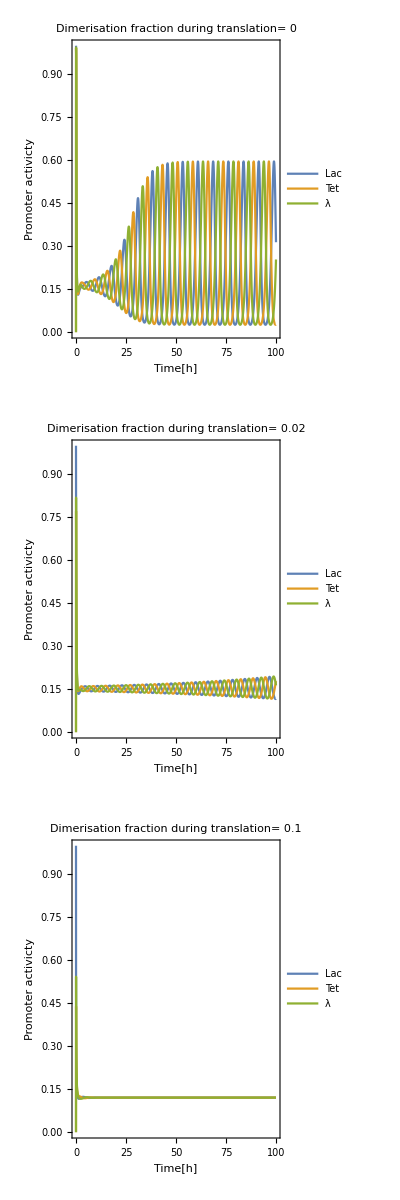

```mathematica
SystemOpen["solutions.pdf"]
```

```mathematica
SystemOpen["solutions.pdf"]
```

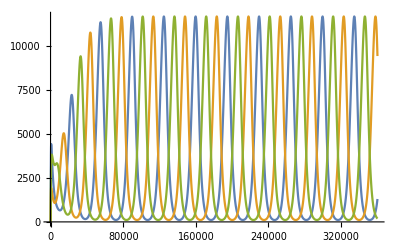

```mathematica
NDSolveValue[Join[system,{m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}]/.{kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.005,α->0 1,kdim-> .00000001},{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},{t,0,500000}][[;;3]]//Plot[#,{t,0,360000}]&
```

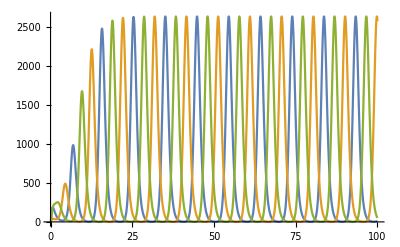

{m1[t]→1,m2[t]→1,m3[t]→1,m12[t]→1,m22[t]→1,m32[t]→1,p1[t]→1,p2[t]→1,p3[t]→1,kun→1,ks→1,kdm→1,kon→1,kdim→1}

```mathematica
NDSolveValue[Join[system,{m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}]/.{kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.005,α->0 1,kdim-> .00000001},{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},{t,0,500000}][[4;;6]]//Plot[Evaluate[#/.t-> 3600τ],{τ,0,100}]&
```

```mathematica
system[[;;,2]]
```

```mathematica
{kun (1-p1[t])-ks m32[t] p1[t],-kdm m1[t]+kon (1-α) p1[t],kdim m1[t]^2-kdm m12[t]+kon α p1[t],kun (1-p2[t])-ks m12[t] p2[t],-kdm m2[t]+kon (1-α) p2[t],kdim m2[t]^2-kdm m22[t]+kon α p2[t],kun (1-p3[t])-ks m22[t] p3[t],-kdm m3[t]+kon (1-α) p3[t],kdim m3[t]^2-kdm m32[t]+kon α p3[t]}/.(#-> 1&/@{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t],kun,ks,kdm,kon,kdim,α})
```

{-1,-α,α,-1,-α,α,-1,-α,α}

{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t],kun,ks,kdm,kon,kdim}→0

```mathematica
steadystate=Solve[system[[;;,2]]==0, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},PositiveReals]
```

$Aborted

```mathematica
steadystate=Solve[system[[;;,2]]==0, {p1[t],p2[t],p3[t]},PositiveReals]
```

{}

```mathematica
0∈NonNegativeReals
```

True

```mathematica
steadystate
```

{}

```mathematica
steadystate=Solve[{system[[;;,2]]==0,p1[t]>0  (*removes trivial solution*),{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t],kun,ks,kdm,kon,kdim,α}∈PositiveReals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},PositiveReals][[1]]
```

$Aborted

```mathematica
jacobian=D[system[[;;,2]], {{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}}];jacobian//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -ks p1[t] | -kun-ks m32[t] | 0 | 0
-kdm-2 kdim m1[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α) | 0 | 0
2 kdim m1[t] | 0 | 0 | -kdm | 0 | 0 | kon α | 0 | 0
0 | 0 | 0 | -ks p2[t] | 0 | 0 | 0 | -kun-ks m12[t] | 0
0 | -kdm-2 kdim m2[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α) | 0
0 | 2 kdim m2[t] | 0 | 0 | -kdm | 0 | 0 | kon α | 0
0 | 0 | 0 | 0 | -ks p3[t] | 0 | 0 | 0 | -kun-ks m22[t]
0 | 0 | -kdm-2 kdim m3[t] | 0 | 0 | 0 | 0 | 0 | kon (1-α)
0 | 0 | 2 kdim m3[t] | 0 | 0 | -kdm | 0 | 0 | kon α)

```mathematica
Trivial
```

```mathematica
steadystate=Solve[{system[[;;,2]]==0/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/10,kun->20},p1[t]>0  (*removes trivial solution*),{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}∈Reals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
Solve[{Evaluate[system[[;;,2]]==0/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/10,kun->20,α->0.1}],p1[t]>0  (*removes trivial solution*),{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}∈Reals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}]
```

{{m1[t]→2.53586,m2[t]→2.53586,m3[t]→2.53586,m12[t]→1929.46,m22[t]→1929.46,m32[t]→1929.46,p1[t]→0.0939207,p2[t]→0.0939207,p3[t]→0.0939207}}

```mathematica
Eigenvalues[jacobian/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/10,kun->20,α->a}/.replacements[[1]]];
```

```mathematica
replacements=Table[Eigenvalues[Evaluate[jacobian/.{kon-> .1,kdm-> 1./5/60,ks-> 1./10,kun->20.,α->a}]/.First[Solve[{Evaluate[system[[;;,2]]==0/.{kon-> .1,kdm-> 1./5/60,ks-> 1./10,kun->20.,α->a}],p1[t]>0  (*removes trivial solution*),{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}∈Reals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}]]],{a,Subdivide[0,1,20][[;;-2]]}];
```

```mathematica
Subdivide[0,1,20][[;;-2]]
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20}

```mathematica
ComplexPlot
```

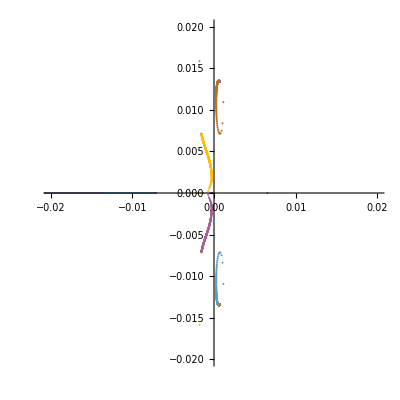

```mathematica
ComplexListPlot[replacements=Table[If[Head[#]===List,#,Nothing]&@Eigenvalues[Evaluate[jacobian/.{kon->1,kdm-> 1/5/60,ks-> 1./10,kun->20.,α->a}]/.First[Solve[{Evaluate[system[[;;,2]]==0/.{kon-> .1,kdm-> 1./5/60,ks-> 1./10,kun->20.,α->a}],p1[t]>0  (*removes trivial solution*),{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}∈Reals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}]]],{a,Subdivide[0,1,500]}]ᵀ,Joined->False,PlotRange->{{-0.02,0.02},{-0.02,0.02}}]
```

```mathematica
pars={kon-> 10,kdm-> 1/40/60,ks-> 1/1200,kun->0.005,kdim-> .00000001};
```

```mathematica
sys:=system[[;;,2]]
```

```mathematica
solut[a_]:=((*Print[a];*)
Solve[{system[[;;,2]]==0/.pars,{m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}∈PositiveReals}, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]},PositiveReals][[1]])
```

```mathematica
solut[a_?NumberQ]:=solut[a]=(NotebookDelete[temp];temp=PrintTemporary[a];Solve[system[[;;,2]]==0/.pars/.α-> a, {m1[t],m2[t],m3[t],m12[t],m22[t],m32[t],p1[t],p2[t],p3[t]}])
```

```mathematica
solut[0.1];
```

```mathematica
eig={Re[#],Im[#]}&/@Eigenvalues[jacobian];
```

```mathematica
solut[j]
```

j

$Aborted

```mathematica
eig2[j]
```

eig2[j]

```mathematica
NumberQ[j]
```

False

```mathematica
f[1]
```

j

Sin[1]

```mathematica
NMaximize
```

```mathematica
f[x_?NumberQ]:=(Print[j];Sin[x])
```

```mathematica
test2[a_]:=(Print[a];Sin[a])
```

```mathematica
test[a_]:=(Print[a];test2[N[a]])
```

```mathematica
Root
```

```mathematica
Table[eig2[a][[-1,-1]],{a,0,1,.1}]
```

0.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

```mathematica
eig2[0.1]
```

0.1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{-0.0625518,0},{-0.000207542,0},{4.21254×10^-7,0},{0.0791255,0},{0.996117,0},{-0.0100941,-0.0337357},{-0.0100941,0.0337357},{0.0038524,-0.0137789},{0.0038524,0.0137789}}

```mathematica
eig2[x]
```

eig2[x]

```mathematica
Monitor
```

Plot::invmaxrec: MaxRecursion must be a non-negative integer; the recursion value is limited to 15. Using MaxRecursion -> 15.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

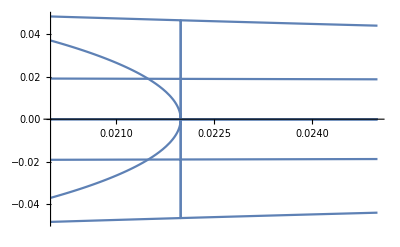

```mathematica
Plot[(eig2[a][[;;,-1]]),{a,0.02,.025},PlotPoints->100,MaxRecursion->∞]
```

```mathematica
eig2[a][[;;,-1]]
```

Part::partd: Part specification eig2[a]⟦1;;All,-1⟧ is longer than depth of object.

eig2[a]⟦1;;All,-1⟧

```mathematica
eig1/.α->0/.pars/.(solut[0][[1]])
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.0240931,-0.000208365,3.78697×10^-7,-0.0712128-0.0713208 ⅈ,-0.0712128+0.0713208 ⅈ,0.012029-0.0208711 ⅈ,0.012029+0.0208711 ⅈ,0.0713343-0.0712217 ⅈ,0.0713343+0.0712217 ⅈ}

```mathematica
Remove[eig12];
```

```mathematica
eig12[a_?NumberQ]:=eig12[a]=(eig1/.α->a/.pars/.(solut[a][[1]]))
```

```mathematica
Eigenvalues[jacobian];
```

```mathematica
Remove[eig2]
```

```mathematica
ReImPlot[{eig12},{a,.02,.025},PlotPoints->4,MaxRecursion->0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

```mathematica
eig1=Eigenvalues[jacobian][[-2;;]];
```

```mathematica
Eigenvalues[jacobian]/.α->a/.pars/.(solut[a][[1]])
```

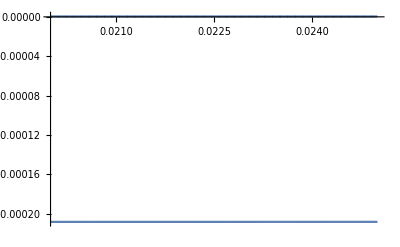

```mathematica
ReImPlot[Eigenvalues[jacobian][[{2,3}]]/.α->a/.pars/.(solut[a][[1]]),{a,.02,.025}]
```

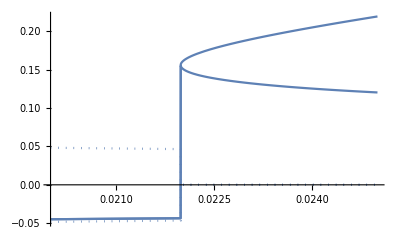

```mathematica
ReImPlot[Eigenvalues[jacobian][[{4,5}]]/.α->a/.pars/.(solut[a][[1]]),{a,.02,.025}]
```

```mathematica
ReImPlot[Eigenvalues[jacobian][[{6,7}]]/.α->a/.pars/.(solut[a][[1]]),{a,0,.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

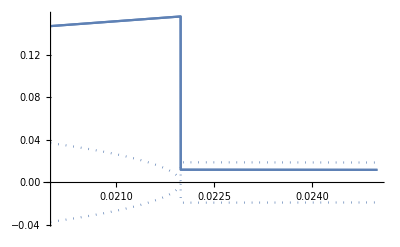

```mathematica
ReImPlot[Eigenvalues[jacobian][[{8,9}]]/.α->a/.pars/.(solut[a][[1]]),{a,.02,.025}]
```

```mathematica
0<0.4<1
```

True

```mathematica
Remove[test]
```

```mathematica
ParametricPlot[(*Echo[*)eig2[a],{a,0.,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},MaxRecursion->15,PlotPoints->100(*,MaxRecursion->0,PlotPoints->10*)]
```

```mathematica
test[a_?NumberQ]:=test[a]=Re[(Eigenvalues[jacobian][[6]])/.α->a/.pars/.(solut[a][[1]])]
```

```mathematica
FindRoot[test[x],{x,0.022}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{x→0.812205}

```mathematica
test[0.812205]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.59419×10^-10

```mathematica
Solve[test[x]==0,x]
```

$Aborted

```mathematica
Solve[Re[Eigenvalues[jacobian][[8]]]==0,a]
```

{}

```mathematica
Solve[Re[Eigenvalues[jacobian][[8]]/.α->a/.pars/.(solut[a][[1]])]==0,a]
```

ReplaceAll::reps: {a} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

```mathematica
ReImPlot[Eigenvalues[jacobian][[{8,9}]]/.α->a/.pars/.(solut[a][[1]]),{a,.02,.025}]
```

-Graphics-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

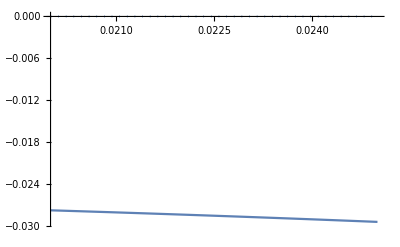
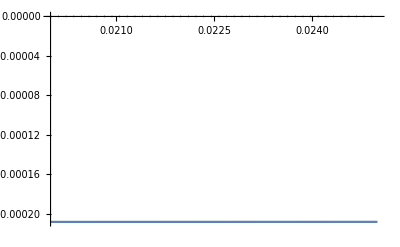
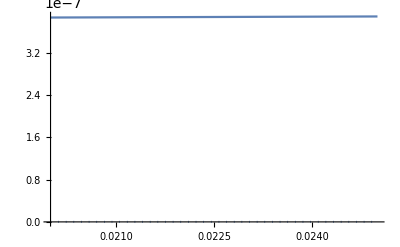
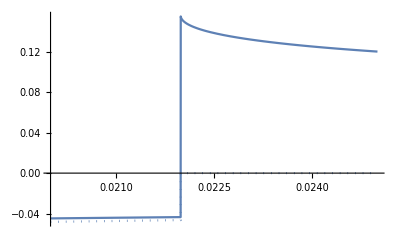
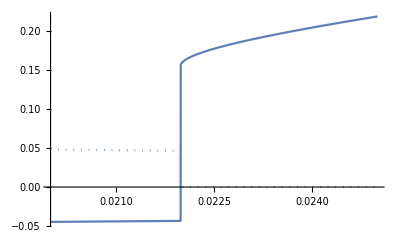
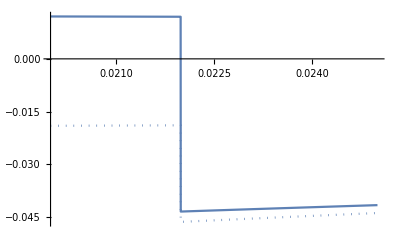
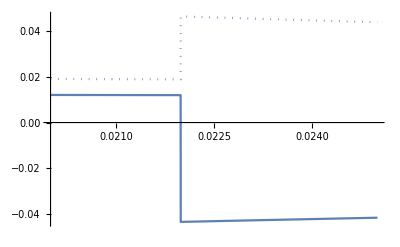
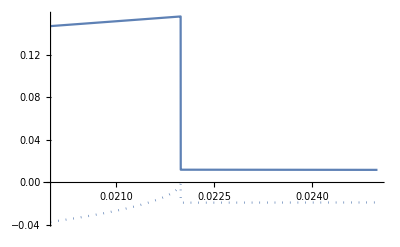

```mathematica
Sh
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

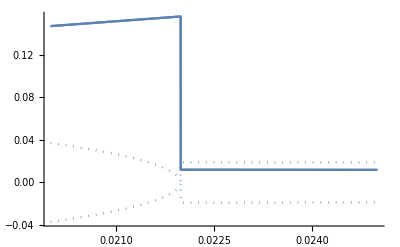

```mathematica
ReImPlot[eig12[a],{a,.02,.025},PlotRange->All]
```

```mathematica
Export["Oscilatory_analasys.pdf",%96]
```

Oscilatory_analasys.pdf

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

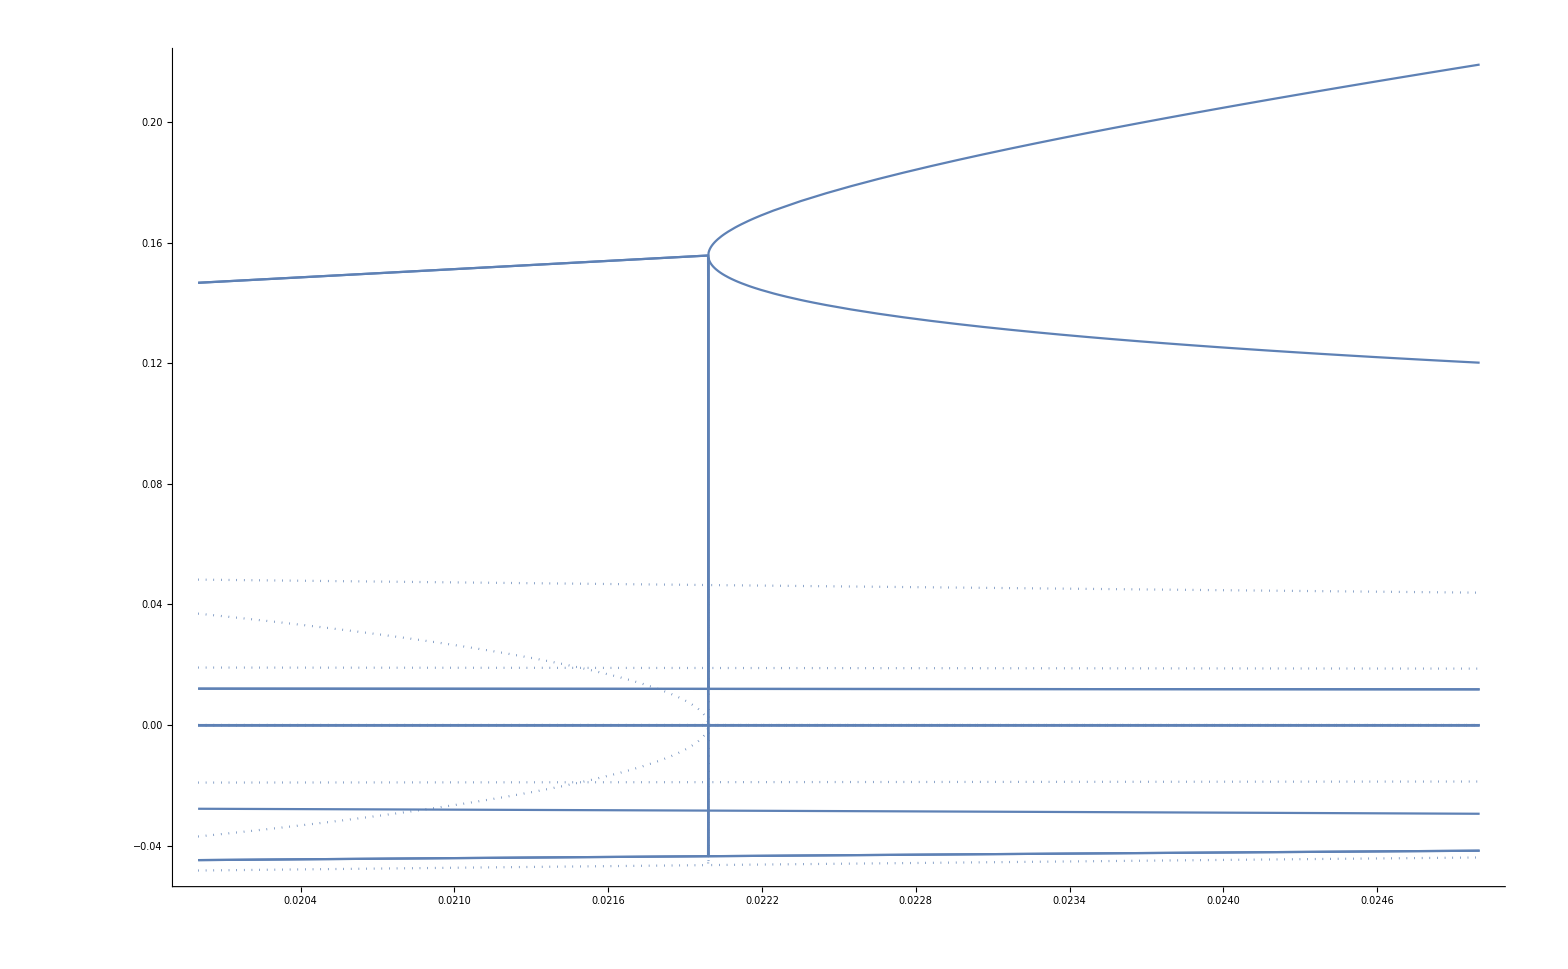

```mathematica
ReImPlot[eig12[a],{a,.02,.025},PlotRange->All]
```

```mathematica
eig2[a_?NumberQ]:=eig2[a]=(eig/.α->a/.pars/.(solut[a][[1]]))[[;;,1]]
```

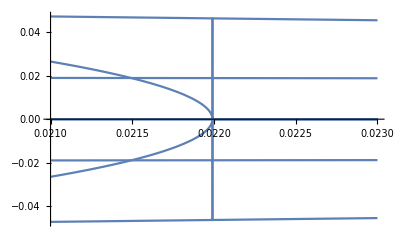

```mathematica
Plot[eig2[a],{a,0.021,.023},Evaluated->True]
```

```mathematica
eig={Re[#],Im[#]}&/@Eigenvalues[jacobian];
```

Plot::invmaxrec: MaxRecursion must be a non-negative integer; the recursion value is limited to 15. Using MaxRecursion -> 15.

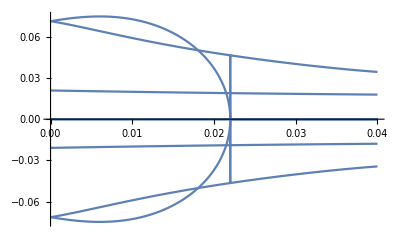

```mathematica
Plot[eig2[a][[;;,-1]],{a,0,.04},PlotPoints->200,MaxRecursion->Infinity]
```

Plot::invmaxrec: MaxRecursion must be a non-negative integer; the recursion value is limited to 15. Using MaxRecursion -> 15.

2.51508×10^-6

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

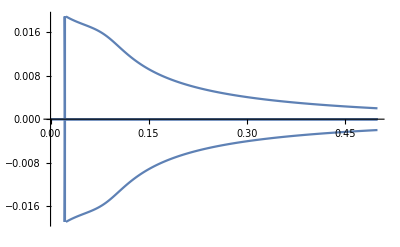

```mathematica
Plot[eig2[a][[;;,-1]],{a,0,.5},PlotPoints->200,MaxRecursion->Infinity]
```

```mathematica
FindRoot[eig2[a][[-1,-1]]==0,{a,0.1}]
```

Part::partd: Part specification eig2[a]⟦-1,-1⟧ is longer than depth of object.

0.1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.22675

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

$Aborted

```mathematica
ParametricPlot[(*Echo[*)#,{a,0.,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},MaxRecursion->15,PlotPoints->100(*,MaxRecursion->0,PlotPoints->10*)]&/@eig2[a]
```

a

$Aborted

```mathematica
ParametricPlot[(*Echo[*)eig2[a],{a,0.,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},MaxRecursion->15,PlotPoints->100(*,MaxRecursion->0,PlotPoints->10*)]
```

0.

0.000010101

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

```mathematica
ParametricPlot[(*Echo[*)eig2[a],{a,0.,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},MaxRecursion->15,PlotPoints->100(*,MaxRecursion->0,PlotPoints->10*)]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ParametricPlot[(*Echo[*)eig2[a],{a,0.,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},MaxRecursion->15,PlotPoints->100(*,MaxRecursion->0,PlotPoints->10*)]
```

```mathematica
~
```

```mathematica
.
```

```mathematica
ParametricPlot[{Re[#],Im[#]},{α,0,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotLegends->Automatic,PlotRange->{{-0.02,0.02},{-0.02,0.02}},Frame->True,FrameLabel->{"Real component eigenvalues","Imaginary component eigenvalues"},WorkingPrecision->20,MaxRecursion->15,PlotPoints->500]&/@(Eigenvalues[jacobian/.steadystate[[2]]/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Eigenvectors[jacobian/.steadystate[[2]]/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200,α->0.5}])//TableForm
```

0.0146792+0. ⅈ | -0.0416481+0. ⅈ | -0.0381316+0. ⅈ | -0.0542473+0. ⅈ | 0.533845+0. ⅈ | 0.496798+0. ⅈ | -0.0379908+0. ⅈ | 0.496733+0. ⅈ | 0.462242+0. ⅈ
-0.0302864+0. ⅈ | -0.106647+0. ⅈ | -0.124987+0. ⅈ | 0.0854208+0. ⅈ | -0.765844+0. ⅈ | -0.570715+0. ⅈ | -0.0312189+0. ⅈ | -0.216798+0. ⅈ | -0.0676916+0. ⅈ
-0.0687973+0. ⅈ | 0.0910139+0. ⅈ | 0.0715678+0. ⅈ | -0.0541259+0. ⅈ | 0.605203+0. ⅈ | 0.765585+0. ⅈ | -0.0286304+0. ⅈ | -0.153814+0. ⅈ | 0.0454055+0. ⅈ
-0.0691994+0.028253 ⅈ | 0.690272+0. ⅈ | 0.660848+0.00328441 ⅈ | 0.027138+0.0389277 ⅈ | -0.190057-0.0198041 ⅈ | -0.177314+0.00428848 ⅈ | -0.00666008+0.0772667 ⅈ | 0.0487444-0.020697 ⅈ | 0.0461723+0.00560361 ⅈ
-0.0691994-0.028253 ⅈ | 0.690272+0. ⅈ | 0.660848-0.00328441 ⅈ | 0.027138-0.0389277 ⅈ | -0.190057+0.0198041 ⅈ | -0.177314-0.00428848 ⅈ | -0.00666008-0.0772667 ⅈ | 0.0487444+0.020697 ⅈ | 0.0461723-0.00560361 ⅈ
-0.119827+0. ⅈ | 0.522603+0. ⅈ | 0.7243+0. ⅈ | -0.138504+0. ⅈ | 0.3247+0. ⅈ | -0.239203+0. ⅈ | 0.0228356+0. ⅈ | 0.0539916+0. ⅈ | 0.0514712+0. ⅈ
-0.185922+0.0630142 ⅈ | -0.336468+0.212482 ⅈ | 0.773262+0. ⅈ | -0.236195-0.112624 ⅈ | 0.237485-0.00410542 ⅈ | -0.276816-0.0050893 ⅈ | -0.0196976+0.00475681 ⅈ | -0.0185337+0.0161453 ⅈ | 0.0511103+0.000102841 ⅈ
-0.185922-0.0630142 ⅈ | -0.336468-0.212482 ⅈ | 0.773262+0. ⅈ | -0.236195+0.112624 ⅈ | 0.237485+0.00410542 ⅈ | -0.276816+0.0050893 ⅈ | -0.0196976-0.00475681 ⅈ | -0.0185337-0.0161453 ⅈ | 0.0511103-0.000102841 ⅈ
0.746991+0. ⅈ | -0.462677+0. ⅈ | 0.426373+0. ⅈ | -0.103905+0. ⅈ | 0.114041+0. ⅈ | -0.132192+0. ⅈ | 0.0548333+0. ⅈ | -0.0320859+0. ⅈ | 0.028774+0. ⅈ

```mathematica
Colo
```

```mathematica
ColorData["M10DefaultDensityGradient"]
```

ColorDataFunction[…]

```mathematica
BarLegend["M10DefaultDensityGradient"]
```

```mathematica
ParametricPlot[{Re[#],Im[#]}&/@(waardes/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200}),{α,0,1},ColorFunction->(ColorData["M10DefaultDensityGradient"][#3]&),ColorFunctionScaling->False,PlotLegends->BarLegend["M10DefaultDensityGradient"],PlotRange->All,PlotPoints->2,MaxRecursion->0]
```

-Graphics-

```mathematica
Show[Table[ListPlot[({Re[#],Im[#]}&/@(waardes/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200,α->test})),PlotMarkers->test],{test,0,1,0.1}]]
```

```mathematica
Im
```

```mathematica
Manipulate[Evaluate[ListPlot[{Re[#],Im[#]}&/@(waardes/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200,α->α2})]],{α2,0,1}]
```

```mathematica
Manipulate[GraphicsColumn[{ListPlot[{Re[#],Im[#]}&/@(Eigenvalues[/.#//.{α1-> .13,α2-> .13,λ1-> 1/30,λ2-> 1/30,β1-> b1,β2->b2,β3->b3,β4->b4}])],ListPlot[{{f,g}}/.#]}]&@(ss//.{α1-> .13,α2-> .13,λ1-> 1/30,λ2-> 1/30,β1-> b1,β2->b2,β3->b3,β4->b4}),{{b1,.01},0,1},{{b2,0.04},0,1},{{b3,.01},0,1},{{b4,0.04},0,1},{{b5,0.2},0,1}]
```

```mathematica
1/(kdm^2 kun)Root[kdm^11 ks kun^4-2 kdm^10 kon ks kun^4+kdm^9 kon^2 ks kun^4+0 #1+kdm^2 kun^2 #1^3+#1^4&,1]//FullSimplify
```

Root[kdm^11 ks kun^4-2 kdm^10 kon ks kun^4+kdm^9 kon^2 ks kun^4+kdm^2 kun^2 #1^3+#1^4&,1]/(kdm^2 kun)

```mathematica
Solve[D[p1[t], t]==ks m32[t]- kun p1[t]==0,P1[t]]
```

```mathematica
2 kdm^5 kon ks^2 kun^2-2 kdm^4 kon^2 ks^2 kun^2 ==0
```

2 kdm^5 kon ks^2 kun^2-2 kdm^4 kon^2 ks^2 kun^2==0

```mathematica
Join[system,{m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}]/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200,α->0.5}
```

{p1'[t]==m32[t]/1000-p1[t]/200,m1'[t]==-m1[t]/300+0.05 p1[t],m12'[t]==m1[t]^2-m12[t]/300+0.05 p1[t],p2'[t]==m12[t]/1000-p2[t]/200,m2'[t]==-m2[t]/300+0.05 p2[t],m22'[t]==m2[t]^2-m22[t]/300+0.05 p2[t],p3'[t]==m22[t]/1000-p3[t]/200,m3'[t]==-m3[t]/300+0.05 p3[t],m32'[t]==m3[t]^2-m32[t]/300+0.05 p3[t],m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0}

DSolve[{p1'[t]==m32[t]/1000+1/200 (-1+p1[t]),m1'[t]==-m1[t]/300+0.05 p1[t],m12'[t]==m1[t]^2-m12[t]/300+0.05 p1[t],p2'[t]==m12[t]/1000+1/200 (-1+p2[t]),m2'[t]==-m2[t]/300+0.05 p2[t],m22'[t]==m2[t]^2-m22[t]/300+0.05 p2[t],p3'[t]==m22[t]/1000+1/200 (-1+p3[t]),m3'[t]==-m3[t]/300+0.05 p3[t],m32'[t]==m3[t]^2-m32[t]/300+0.05 p3[t],m1[0]==0,m12[0]==0,m2[0]==0,m22[0]==0,m3[0]==0,m32[0]==0,p1[0]==1,p2[0]==0,p3[0]==0},{m1[t],m12[t],m2[t],m22[t],m3[t],m32[t],p1[t],p2[t],p3[t]},{t}]

```mathematica
DSolve[%81,{m1[t],m12[t],m2[t],m22[t],m3[t],m32[t],p1[t],p2[t],p3[t]},{t}]
```

DSolve[{p1'[t]==m32[t]/1000-p1[t]/200,m1'[t]==-m1[t]/300+0.05 p1[t],m12'[t]==m1[t]^2-m12[t]/300+0.05 p1[t],p2'[t]==m12[t]/1000-p2[t]/200,m2'[t]==-m2[t]/300+0.05 p2[t],m22'[t]==m2[t]^2-m22[t]/300+0.05 p2[t],p3'[t]==m22[t]/1000-p3[t]/200,m3'[t]==-m3[t]/300+0.05 p3[t],m32'[t]==m3[t]^2-m32[t]/300+0.05 p3[t]},{m1[t],m12[t],m2[t],m22[t],m3[t],m32[t],p1[t],p2[t],p3[t]},{t}]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

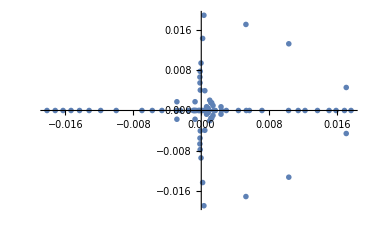

```mathematica
Show[Table[ListPlot[({Re[#],Im[#]}&/@(waardes/.{kon-> 1/10,kdm-> 1/5/60,ks-> 1/1000,kun->1/200,α->test})),PlotMarkers->test],{test,0,1,0.1}]]
```

```mathematica
1.
```

1.